## Definition of constants

### Planck constant - J s

```mathematica
h=6.62606957 10^-34
```

6.62607×10^-34

### Speed of light - m/s

```mathematica
c=299792458
```

299792458

### Boltzmann constant - J/K

```mathematica
k=1.3806488 10^-23
```

1.38065×10^-23

### Pre - computation of hc

```mathematica
hc=h c
```

1.98645×10^-25

### Stefan-Boltzmann constant

```mathematica
σ=5.670373 10^-8
```

5.67037×10^-8

### Constant of proportionality

```mathematica
bWien=2.8977721×10^(−3)
```

0.00289777

### General constants substitution

```mathematica
a=2 h c^2
```

1.19104×10^-16

```mathematica
b=h c /k
```

0.0143878

```mathematica
font="CMU serif";
fontSize=22;
TASIColor=RGBColor[0,0.917,0.576];
TASIColor=RGBColor[1,0,0];
ASTERColor=RGBColor[1,(*0,0*)0.51,0.196];
AHSColor=RGBColor[0,0.635,0.91];
(*approxFun[par1_,par2_,var_]:=1/(par1 var^3+par2);*)
(*approxFun[par1_,par2_,var_]:=par1 var^2+par2;*)
approxFun[par1_,par2_,var_]:=par1 var+par2;
lineThickness=0.01;
```

## Planck’s functions

### Basic functions

#### Wien’s displacement law

```mathematica
WienLawFunction[T_]:=bWien/T
```

#### Planck’s law

```mathematica
PlanckLawFunction[T_,λ_]:=(a)/(λ^5(Exp[b / (λ T)]-1))
```

#### Inverse Planck’s law

```mathematica
InversePlanckLawFunction[R_,λ_,emis_]:=(b)/(λ Log[(a emis)/(λ^5 R)+1])
```

## Chapter 1

```mathematica
temp=300;
```

```mathematica
quartzData=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/quartz.txt","Data"];
quartzDataNew=ConstantArray[0,Dimensions[quartzData]];
quartzDataNew[[;;,1]]=quartzData[[;;,1]];
quartzDataNew[[;;,2]]=1-quartzData[[;;,2]]/100;
```

```mathematica
Plot[Interpolation[quartzDataNew,Method->"Spline"][x],{x,7.5,13.5},
PlotStyle->{RGBColor[{108,91,123}/255],Thickness[0.008]},
PlotRange->{All,{Automatic,1.005}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Emissivity",""},{"Wavelength (µm)","Quartz emissivity"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

-Graphics-

```mathematica
planckData300=Table[{x 10^6,PlanckLawFunction[300,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
planckData290=Table[{x 10^6,PlanckLawFunction[290,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
planckData310=Table[{x 10^6,PlanckLawFunction[310,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
tmp1={250,208,137}/255;
tmp2={255,156,91}/255;
tmp3={245,99,74}/255;
color1=RGBColor[tmp1];
color2=RGBColor[tmp2];
color3=RGBColor[tmp3];
```

```mathematica
Plot[{Interpolation[planckData310][x],Interpolation[planckData300][x],Interpolation[planckData290][x]},{x,7.5,13.5},
(*PlotStyle->Directive[{{Red,Green,Blue},Thickness[0.01]}],*)
PlotStyle->{Directive[color3,Thickness[0.008]],Directive[color2,Thickness[0.008]],Directive[color1,Thickness[0.008]]},
PlotRange->{{Automatic,Automatic},{6.5,14.0}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
(*FrameTicks->{{#,1000000 #}&/@FindDivisions[{0.00002,.000002},20],{#, 0.000001#}&/@FindDivisions[{1000000,10000000},20]},*)
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Planck's law"}},
PlotLegends->Placed[LineLegend[{"310 K","300 K","290 K"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.76}],
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

Plot::prng: Value of option PlotRange -> {{Automatic, Automatic}, {6.5, 14.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
quartzData=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_Thesis/pics/Fig_Gen_Bundle/quartz.txt","Data"];
quartzData[[;;,1]]=quartzData[[;;,1]] 10^-6;
quartzData[[;;,2]]=1-quartzData[[;;,2]]/100;
eB290=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[290,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
eB300=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[300,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
eB310=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[310,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
```

```mathematica
Plot[{Interpolation[eB310,Method->"Spline"][x],Interpolation[eB300,Method->"Spline"][x],Interpolation[eB290,Method->"Spline"][x]},{x,7.5,13.5},
PlotStyle->{Directive[color3,Thickness[0.008]],Directive[color2,Thickness[0.008]],Directive[color1,Thickness[0.008]]},
PlotRange->{All,{6.5,14}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Quartz radiance"}},
PlotLegends->Placed[LineLegend[{"310 K","300 K","290 K"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.76}],
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

-Graphics-

## Chapter 1I

### TASI Response Functions

```mathematica
TASIBandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250} 10^-9;
```

```mathematica
TASIFWHM=109.5 10^-9;
```

```mathematica
tmpTASIdata=
Table[
Table[
{x 10^6,Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)]}
,{x,TASIBandCenters[[i]]-1.5475*10^-7,TASIBandCenters[[i]]+1.5475*10^-7,0.001 10^-6}]
,{i,1,32}];
```

```mathematica
TASIResponseFunction[bandn_,x_]:=Table[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{i,1,Length[TASIBandCenters]}][[bandn]]
```

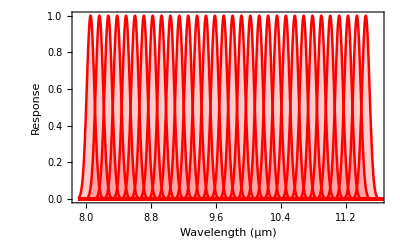

```mathematica
Show[
Table[
Plot[Exp[-(x 10^-6-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.9 ,11.7},
PlotRange->{{7.9,11.6},All},
PlotStyle->{TASIColor,Thickness[0.0045]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.20],TASIColor]
],{i,1,Length[TASIBandCenters]}],
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Response",""},{"Wavelength (µm)","TASI Response Functions"}},
AspectRatio->0.6,
ImageSize->{Automatic,180},
Frame->True,
FrameStyle->Black
]
```

```mathematica
quartzData=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/quartz.txt","Data"];
quartzData[[;;,1]]=quartzData[[;;,1]] 10^-6;
quartzData[[;;,2]]=1-quartzData[[;;,2]]/100;
eB=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[temp,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
```

```mathematica
data=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]PlanckLawFunction[temp,quartzData[[k,1]]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
data[[;;,1]]=data[[;;,1]] 10^6;
data[[;;,2]]=data[[;;,2]] 10^-6;
```

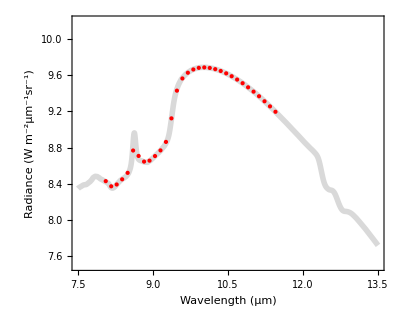

```mathematica
Show[
Plot[Interpolation[eB,Method->"Spline"][x],{x,7.5,13.5},
PlotStyle->{LightGray,Thickness[0.01]},PlotRange->{All,{7.5,10.2}}
],
ListPlot[data,PlotStyle->TASIColor,PlotRange->{All,{7.5,10.2}}],
PlotRange->{All,{7.5,10.2}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.8,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Quartz radiance by TASI"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

### Data for radiometric calibrations, DN coeff computation and atmospheric correction

```mathematica
wavelengths=LmDataForComputationOfCalibCoef[[1,;;]]=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/dataForCalibProc/Lm/01_rad.txt","Data"][[;;,1]] 10^-9;

DNdataForComputationOfCalibCoef=ConstantArray[0,{2,32}];
tmpDNdataForComputationOfCalibCoef=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/dataForCalibProc/DN/01_DN.txt","Data"][[;;,2]];
DNdataForComputationOfCalibCoef[[1,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpDNdataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
tmpDNdataForComputationOfCalibCoef=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/dataForCalibProc/DN/02_DN.txt","Data"][[;;,2]];
DNdataForComputationOfCalibCoef[[2,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpDNdataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

LmDataForComputationOfCalibCoef=ConstantArray[0,{2,32}];
tmpLmDataForComputationOfCalibCoef=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/dataForCalibProc/Lm/01_rad.txt","Data"][[;;,2]]10^4;
LmDataForComputationOfCalibCoef[[1,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpLmDataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
tmpLmDataForComputationOfCalibCoef=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/dataForCalibProc/Lm/02_rad.txt","Data"][[;;,2]]10^4;
LmDataForComputationOfCalibCoef[[2,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpLmDataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

Set::noval: Symbol LmDataForComputationOfCalibCoef in part assignment does not have an immediate value.

```mathematica
calibCoef=Table[{c1,c2}/.NSolve[{DNdataForComputationOfCalibCoef[[1,i,2]]==c1+c2 LmDataForComputationOfCalibCoef[[1,i,2]],DNdataForComputationOfCalibCoef[[2,i,2]]==c1+c2 LmDataForComputationOfCalibCoef[[2,i,2]]},{c1,c2}][[1]],{i,1,Length[TASIBandCenters]}];
```

```mathematica
atmData=Import["/Users/Marek/Dropbox/Skola/_Dizertacka/_manuscript/_thesis/pics/Fig_Gen_Bundle/Brno_summer_day_low_altitude.tp8","Data"][[;;,3;;]];
transmissivity=atmData[[;;,1]];
upwelling=atmData[[;;,2]] 10^6;
downwelling=atmData[[;;,3]]10^6;
```

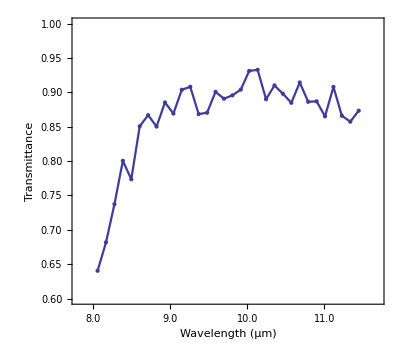

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,transmissivity[[i]]},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,transmissivity[[i]]},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{0.6,1}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Transmittance",SingleLetterItalics->False],""},{"Wavelength (µm)","Transmittance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

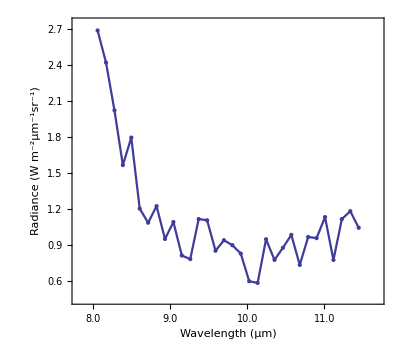

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,upwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,upwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{0.45,2.75}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Upwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

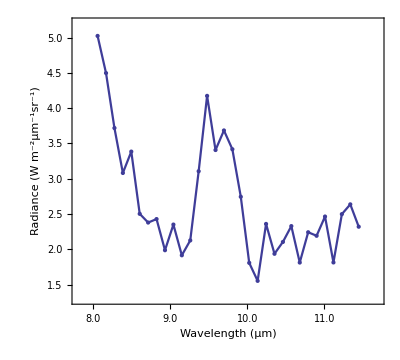

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{1.3,5.2}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Downwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

```mathematica
Table[{TASIBandCenters[[k]]10^6,downwelling[[k]]10^-6+1},{k,1,32,4}]
```

{{8.05475,6.02412},{8.49275,4.38477},{8.93075,2.98704},{9.36875,4.10626},{9.80675,4.41801},{10.2448,3.35968},{10.6828,2.8123},{11.1208,2.81368}}

```mathematica
TASIBandCenters[[32]]
```

0.0000114493

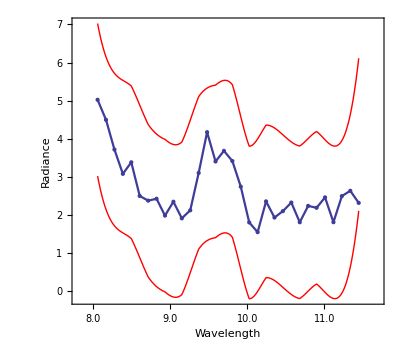

```mathematica
Show[
Plot[Interpolation[Table[{TASIBandCenters[[k]]10^6,downwelling[[k]]10^-6+2},{k,1,32,2}]][x],{x,TASIBandCenters[[1]]10^6,TASIBandCenters[[32]]10^6},PlotStyle->Red],
Plot[Interpolation[Table[{TASIBandCenters[[k]]10^6,downwelling[[k]]10^-6-2},{k,1,32,2}]][x],{x,TASIBandCenters[[1]]10^6,TASIBandCenters[[32]]10^6},PlotStyle->Red],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{Automatic,Automatic}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance",SingleLetterItalics->False],""},{"Wavelength","Downwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

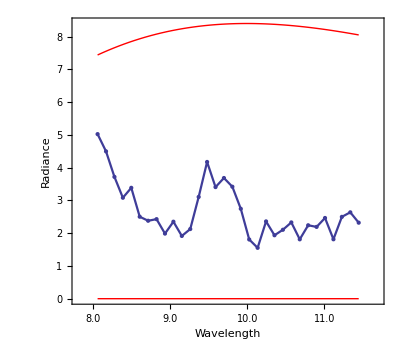

```mathematica
Show[
Plot[Interpolation[Table[{TASIBandCenters[[k]]10^6,PlanckLawFunction[80,TASIBandCenters[[k]]]10^-6},{k,1,32,4}]][x],{x,TASIBandCenters[[1]]10^6,TASIBandCenters[[32]]10^6},PlotStyle->Red],
Plot[Interpolation[Table[{TASIBandCenters[[k]]10^6,PlanckLawFunction[290,TASIBandCenters[[k]]]10^-6},{k,1,32,4}]][x],{x,TASIBandCenters[[1]]10^6,TASIBandCenters[[32]]10^6},PlotStyle->Red],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{Automatic,Automatic}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance",SingleLetterItalics->False],""},{"Wavelength","Downwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

```mathematica
quartzEmissivityByTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
Lq=Table[{TASIBandCenters[[i]],
quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]
},{i,1,Length[TASIBandCenters]}];
Lq[[;;,1]]=Lq[[;;,1]] 10^6;
Lq[[;;,2]]=Lq[[;;,2]] 10^-6;
```

```mathematica
Lm=Table[{TASIBandCenters[[i]],
transmissivity[[i]]quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]+transmissivity[[i]](1-quartzEmissivityByTASI[[i,2]])downwelling[[i]]+upwelling[[i]]
},{i,1,Length[TASIBandCenters]}];
Lm[[;;,1]]=Lm[[;;,1]] 10^6;
Lm[[;;,2]]=Lm[[;;,2]] 10^-6;
```

```mathematica
(*tmp=RGBColor[0,160/255,176/255]*)
(*tmp=RGBColor[1,0,0]*)
(*tmp=RGBColor[1,0.5,0]*)
(*tmp=RGBColor[143/255,190/255,0]*)
```

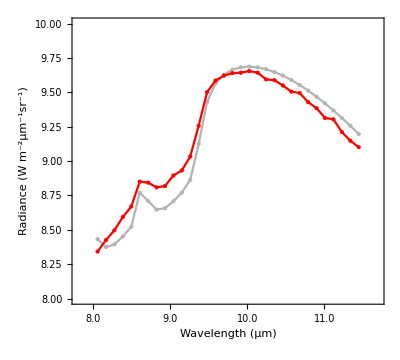

```mathematica
Show[
ListPlot[Lq,Joined->True,PlotStyle->{Thickness[0.004],RGBColor[0.7,0.7,0.7]}],
ListPlot[Lq,PlotStyle->RGBColor[0.7,0.7,0.7]],
ListPlot[Lm,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[Lm,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},{8,10}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","At-sensor radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
(*PlotLegends->Placed[LineLegend[{"At-sensor radiance","Quartz radiance"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.2}],*)
]
```

```mathematica
DN=Table[{TASIBandCenters[[i]],calibCoef[[i,1]]+calibCoef[[i,2]]Lm[[i,2]]},{i,1,Length[TASIBandCenters]}];
DN[[;;,1]]=DN[[;;,1]] 10^6;
```

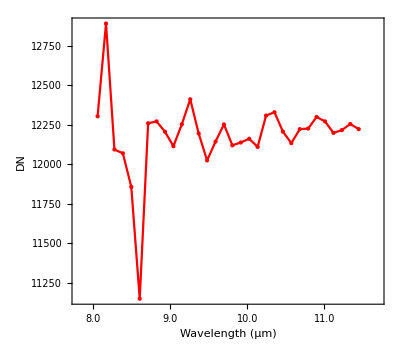

```mathematica
Show[
ListPlot[DN,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[DN,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},All},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["DN",SingleLetterItalics->False],""},{"Wavelength (µm)","Raw data"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

```mathematica
Lll=Table[{TASIBandCenters[[i]],
quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]+(1-quartzEmissivityByTASI[[i,2]])downwelling[[i]]
},{i,1,Length[TASIBandCenters]}];
Lll[[;;,1]]=Lll[[;;,1]] 10^6;
Lll[[;;,2]]=Lll[[;;,2]] 10^-6;
```

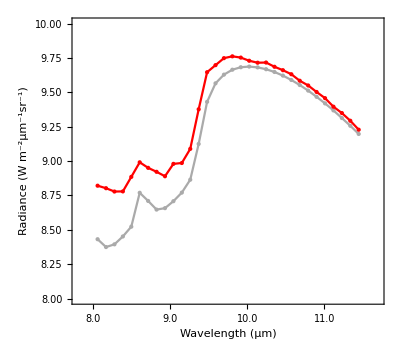

```mathematica
Show[
ListPlot[Lq,Joined->True,PlotStyle->{Thickness[0.004],Lighter[Gray]}],
ListPlot[Lq,PlotStyle->Lighter[Gray]],
ListPlot[Lll,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[Lll,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},{8,10}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Land-leaving radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

### Some testing

```mathematica
Water=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\ASL_reflection_water.txt","Data"];
Water[[;;,1]]=Water[[;;,1]]10^-6;
Water[[;;,2]]=1-Water[[;;,2]]/100;
Water=Table[NIntegrate[Interpolation[Table[{Water[[k,1]],Water[[k,2]]},{k,1,Length[Water]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}],{j,1,Length[TASIBandCenters]}];
(*Water=Water[[6;;27]];*)
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::partd: Part specification Water ⟦ 1 ;; All, 1 ⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::partd: Part specification Water ⟦ 1 ;; All, 2 ⟧ is longer than depth of object.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

NIntegrate::inumr: The integrand ⅇ^-2.31237×10^14\ (-8.05475×10^-6 + λ)^2\ Interpolation[{}][λ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{7.1×10^-6, 3/250000}}.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

NIntegrate::inumr: The integrand ⅇ^-2.31237×10^14\ (-8.05475×10^-6 + λ)^2\ Interpolation[{}][λ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{7.1×10^-6, 3/250000}}.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation :: innd will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^-2.31237×10^14\ (-8.16425×10^-6 + λ)^2\ Interpolation[{}][λ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{7.1×10^-6, 3/250000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

$Aborted

```mathematica
tmpLdown=4 10^6;
```

```mathematica
Manipulate[
Plot[Abs[Water[[band]]-((Water[[band]]PlanckLawFunction[temp,TASIBandCenters[[band]]]+(1-Water[[band]])(tmpLdown+LdownAdd))-(tmpLdown+LdownAdd))/(PlanckLawFunction[temp+tempErr,TASIBandCenters[[band]]]-(tmpLdown+LdownAdd))],{tempErr,-2,2},PlotRange->{{-2,2},{0,0.1}}]
,{{LdownAdd,0},-2 10^6,3 10^6,10^6},{band,1,Length[TASIBandCenters],1}]
```

Part::partd: Part specification Water ⟦ 32 ⟧ is longer than depth of object.

Part::partd: Part specification TASIBandCenters ⟦ 32 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Water ⟦ 32 ⟧ is longer than depth of object.

Part::partd: Part specification TASIBandCenters ⟦ 32 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Water ⟦ 32 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.